```mathematica
1.602 10^-19 300 10^19 //N
```

480.6

```mathematica
ee = 1.602 10^-19;
Ef = 11.7 1.602;
T = 300. 1.3807 10^(- 4)
mu = 1 Ef;
(*k=1.3807·10^23;*)
```

0.041421

```mathematica
foo[mu_] := Block[{}, s = SetPrecision[- (NIntegrate[e √e  1/(Cosh[(e - mu)/T] + 1) (e - mu), {e, 0, Infinity}, MinRecursion->8, AccuracyGoal-> 50])/(NIntegrate[e √e  1/(Cosh[(e - mu)/T] + 1) , {e, 0, Infinity}, MinRecursion->8, AccuracyGoal-> 50]), 50];
Return@s];
foo[ 1 Ef]/480 10^6
```

-0.9410603169096024568698414617765971949362816909949

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
<<MaTeX`
SetDirectory[NotebookDirectory[]]
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.01;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

/home/egor/учеба/тт/3rd/report/pic

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

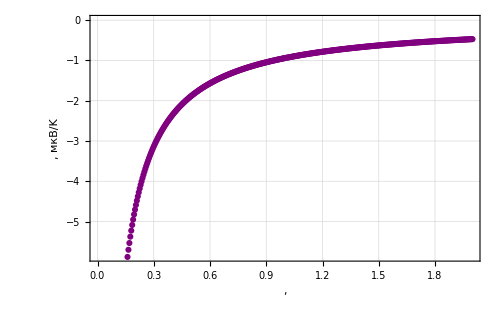

plot.pdf

```mathematica
a = Table[ {x, foo[x Ef ]/480 10^6},{x, 0.0 , 2.0 , 0.005 }];

pl = ListPlot[{#1,#2}&@@@a⟦;;,{1,  2}⟧,

 Ticks-> Automatic,Frame->True,FrameStyle->BlackFrame, 
 GridLines->Automatic, 
 FrameLabel->{  MaTeX["\\mu,  \\varepsilon_F", FontSize->20] "," , "мкВ/K" MaTeX[ "s", FontSize->20] ", "},
GridLines->{grids@0.25,grids@0.1},
PlotRange->{Full, Automatic},
(*AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},*)
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->500,
(*ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],*)
Ticks->{myTicX,Automatic}]


Export["plot.pdf", pl]
```

```mathematica
SetDirectory[NotebookDirectory[]]
aa = Table[ foo[x Ef ]/480 10^6 ,{x, 0.0 , 2.0 , 0.005 }];
aa = ExportString[aa, "RawJSON", "Compact" -> True];
Export["data.txt", aa]
```

/home/egor/учеба/тт/3rd/report/pic

data.txt